## p 37 Evaluating eq 5.15 for g(t)=t

```mathematica
Clear[t,a,b,x,g,f,int]
int=Integrate[(Sqrt[(t-a)(b-t)]t)/(π(x-t)),{t,a,b},PrincipalValue->True]
```

ConditionalExpression[1/(8 √((a-b)^2) π)(-a+b) (-π (a^2-2 a b+b^2+4 a x+4 b x-8 x^2)+4 √(b-x) x √(-a+x) (Log[b-x]-2 Log[-(√(b-x))/(√(-a+x))]-Log[-a+x])), ]

```mathematica
f=(c-(int//Normal))/(π Sqrt[(x-a)(b-x)])//FullSimplify
```

(c-((a-b) (π ((a-b)^2+4 (a+b) x-8 x^2)+4 √(b-x) x √(-a+x) (-Log[b-x]+2 Log[-(√(b-x))/(√(-a+x))]+Log[-a+x])))/(8 √((a-b)^2) π))/(π √((b-x) (-a+x)))

```mathematica
(* evaluate for random numbers *)
Clear[a,b,x,d]
a=RandomReal[];
b=RandomReal[];
If[a>b,
d=b;
b=a;
a=d;
]
x=a+(b-a)*RandomReal[];
(-Log[b-x]+2 Log[-(√(b-x))/(√(-a+x))]+Log[-a+x])-2π I
Clear[a,b,x]
```

0.+0. ⅈ

```mathematica
f=Refine[(-((a-b) (π ((a-b)^2+4 (a+b) x-8 x^2)+4 √(b-x) x √(-a+x) ))/(8 √((a-b)^2) π))/(π √((b-x) (-a+x)))//FullSimplify,{a>0,b>a,b>0,x<b,x>a,x>0,b-x>0}]//FullSimplify
```

((a-b)^2 π+4 (a+b) π x-8 π x^2+4 x √((a-x) (-b+x)))/(8 π^2 √((a-x) (-b+x)))

```mathematica
Integrate[f/(x-xx),{x,a,b},PrincipalValue->True]
```

ConditionalExpression[-(a-b+2 π^2 xx+xx Log[(-a+xx)/(b-xx)])/(2 π^2), Re[b]>xx&&b==Re[b]&&0<Re[a]<xx&&a==Re[a]]

## Eq 5.27

```mathematica
Clear[x,xp,intϵp,intϵm,ϵ]
int=Integrate[Sqrt[2-xp^2]/(π(x-xp)),xp]
```

-(√(2-xp^2)-x ArcSin[xp/(√2)]+√(2-x^2) ArcTanh[(-2+x xp)/(√(2-x^2) √(2-xp^2))])/π

```mathematica
intϵp=int/.{x->x+ϵ};
intϵm=int/.{x->x-ϵ};
```

```mathematica
Limit[intϵm-intϵp//Simplify,ϵ->0,Direction->"FromAbove"]
```

0

```mathematica
Limit[int,xp->-Sqrt[2],Direction->"FromAbove"]
```

-(π x+√(2-x^2) Log[-(2+√2 x)/(√(2-x^2))]-√(2-x^2) Log[(2+√2 x)/(√(2-x^2))])/(2 π)

```mathematica
Limit[int,xp->Sqrt[2],Direction->"FromBelow"]
```

(π x+√(2-x^2) Log[(2-√2 x)/(√(2-x^2))]-√(2-x^2) Log[(-2+√2 x)/(√(2-x^2))])/(2 π)

```mathematica
Clear[x]
res1=((π x+√(2-x^2) Log[(2-√2 x)/(√(2-x^2))]-√(2-x^2) Log[(-2+√2 x)/(√(2-x^2))])/(2 π))-(-(π x+√(2-x^2) Log[-(2+√2 x)/(√(2-x^2))]-√(2-x^2) Log[(2+√2 x)/(√(2-x^2))])/(2 π))//FullSimplify
```

x+(√(2-x^2) (Log[(2-√2 x)/(√(2-x^2))]-Log[(-2+√2 x)/(√(2-x^2))]+Log[-(2+√2 x)/(√(2-x^2))]-Log[(2+√2 x)/(√(2-x^2))]))/(2 π)

```mathematica
(* however the 2nd term is 0 *)
Exp[(Log[(2-√2 x)/(√(2-x^2))]-Log[(-2+√2 x)/(√(2-x^2))]+Log[-(2+√2 x)/(√(2-x^2))]-Log[(2+√2 x)/(√(2-x^2))])]//Simplify
```

1

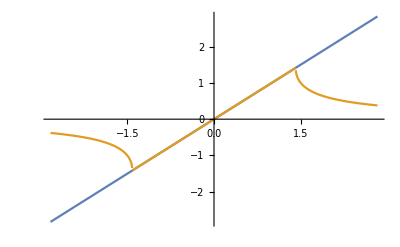

```mathematica
Plot[{x,x+(√(2-x^2) (Log[(2-√2 x)/(√(2-x^2))]-Log[(-2+√2 x)/(√(2-x^2))]+Log[-(2+√2 x)/(√(2-x^2))]-Log[(2+√2 x)/(√(2-x^2))]))/(2 π)},{x,-2√2,+2√2}]
```

```mathematica
(*Integrate[Sqrt[2-xp^2]/(π(x-xp)), {xp ,-√2, +√2}, PrincipalValue->True]*)
```

$Aborted

## 5.33 Catalan numbers

-(2^n (1+(-1)^(2 n)) (Beta[0,1/2+n,3/2]-Beta[1,1/2+n,3/2]))/π

2^-n CatalanNumber[n]

False

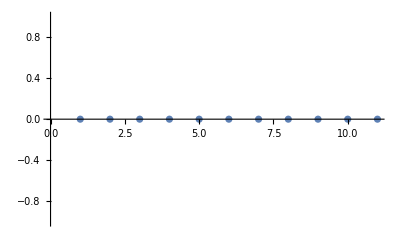

```mathematica
Clear[y,n]
res1=1/π Integrate[y^(2n)Sqrt[2-y^2],{y,-√2,+√2}]
res2=CatalanNumber[n]/2^n(*(1/(n+1)((2n)!)/(n!n!))/2^n*)
(res1-res2)//Simplify;
res1===res2
ListPlot[Table[(res1-res2),{n,0,10,1}]]
```